```mathematica
P1[N_,r1_,r2_,r3_,r0_,t_]:=N r1 r2 r3 r0^2 t^5 /4
```

```mathematica
P2[N_,r1_,r2_,r3_,r0_,b1_,t_]:=3 N r1 r2 r3 r0^2 t^2 Exp[b1 t] /(2 b1 ^3)
```

```mathematica
P3[N_,r1_,r2_,r3_,r0_,b1_,b2_,b12_,t_]:=21.2 N r1 r2 r3 r0^2 (1/(b12^3(b12-b1))+1/(b12^3(b12-b2))+1/(b12^2(b12-b2)^2)) t Exp[b12 t]
```

```mathematica
u = 10.^-8
nAPC=604
np53=83
nKRAS=20
rLOH=10.^-4
```

1.×10^-8

604

83

20

0.0001

```mathematica
nAPC*u
np53*u
nKRAS*u
rLOH
```

6.04×10^-6

8.3×10^-7

2.×10^-7

0.0001

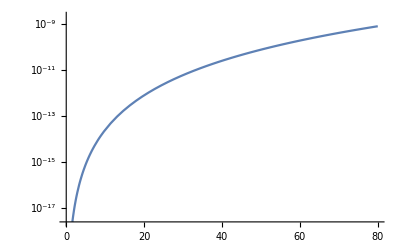

```mathematica
LogPlot[P1[10.^8,6.04 10^-6,8.3 10^-7,2 10^-7,0.0001,t],{t,0,80}]
```

```mathematica
bAPC=0.2
bKRAS=0.07
bBOTH=0.27
```

0.2

0.07

0.27

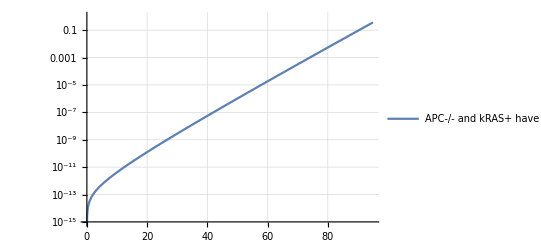

```mathematica
Curves=LogPlot[{P3[10.^8,6.04 10^-6,8.3 10^-7,2 10^-7, 10^-4,0.2,0.07,0.27,t]},{t,0,95},PlotRange->{Automatic,{10.^-15,10^0}},GridLines->Full,PlotLegends->{Style["APC-/- and kRAS+ have adv.",Black,12],LineSpacing->{0, 8}}]
```

```mathematica
P3[10.^8,6.04 10^-6,8.3 10^-7,2 10^-7, 10^-4,0.2,0.07,0.27,81]
```

0.0071691

```mathematica
P3[10.^8,6.04 10^-6,8.3 10^-7,2 10^-7, 10^-4,0.2,0.07,0.27,81]/21.2
```

0.000338165

```mathematica
1/%
```

2957.14

```mathematica
LifetimeRisk={{80,0.007}}
```

{{80,0.007}}

```mathematica
{{80,0.007}}
```

{{80,0.007}}

```mathematica
cross=Graphics[{Line[{{-1,1},{1,-1}}],Line[{{-1,-1},{1,1}}]}];
```

```mathematica
plus=Graphics[{Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}];
```

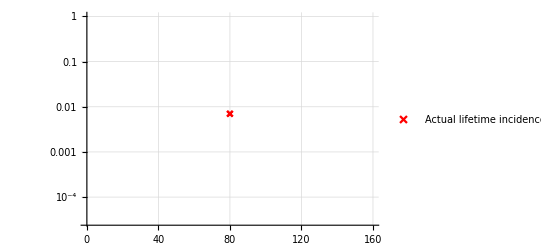

```mathematica
Reallife=ListLogPlot[LifetimeRisk,PlotStyle->Red,PlotMarkers-> {cross,0.03},Axes-> True,GridLines-> Full,PlotLegends->{Style["Actual lifetime incidence, 0.7% (2)",Black,12,LineSpacing->{0, 1}]}]
```

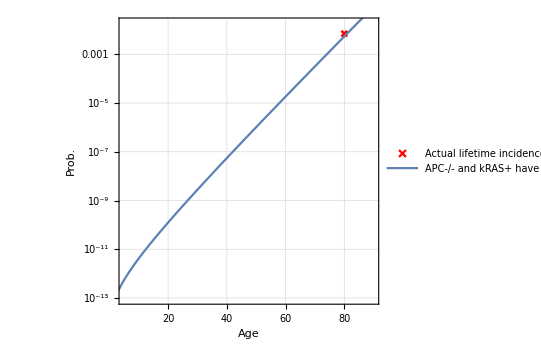

```mathematica
plot=Show[Reallife,Curves,Frame-> True,Axes-> False,FrameLabel->{Style["Age",Black,14],Style["Prob.",Black,14]},PlotRange-> {{5,90},{-30,-4}},AspectRatio-> 0.9]
```

```mathematica
Export["/home/chay/Documents/Academic/Presentations/UW 2019/document/images/LastPlot.pdf",plot]
```

/home/chay/Documents/Academic/Presentations/UW 2019/document/images/LastPlot.pdf

```mathematica
NewSims=Import["/home/chay/Documents/Academic/Papers/Colorectal Adenocarcinoma 2019/timedoutput-tau.csv",{"CSV","Data",All,{1,39}}]
```

```mathematica
OldSims={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,7.99872*^-9},{58,7.99872*^-9},{59,7.99872*^-9},{60,7.99872*^-9},{61,1.59974*^-8},{62,1.59974*^-8},{63,1.59974*^-8},{64,1.59974*^-8},{65,2.39962*^-8},{66,4.79923*^-8},{67,7.99872*^-8},{68,1.03983*^-7},{69,1.35978*^-7},{70,1.75972*^-7},{71,1.99968*^-7},{72,2.31963*^-7},{73,3.03951*^-7},{74,3.59942*^-7},{75,5.11918*^-7},{76,6.71892*^-7},{77,8.55863*^-7},{78,1.06383*^-6},{79,1.35978*^-6}};
```

```mathematica
OldSims=OldSims/.{x_,y_}->{x,y*21.2*100};
```

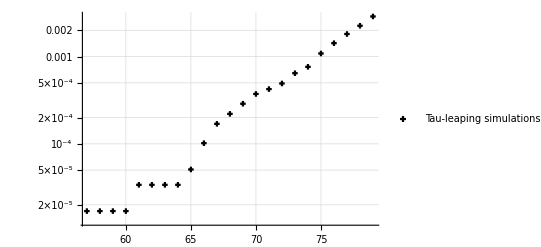

```mathematica
OldSimsPlot=ListLogPlot[OldSims,PlotStyle-> {Black,Thick},PlotMarkers->{plus,0.03},GridLines-> Full,PlotLegends->{Style["Tau-leaping simulations",Black,12,LineSpacing->{0, 8}]}]
```

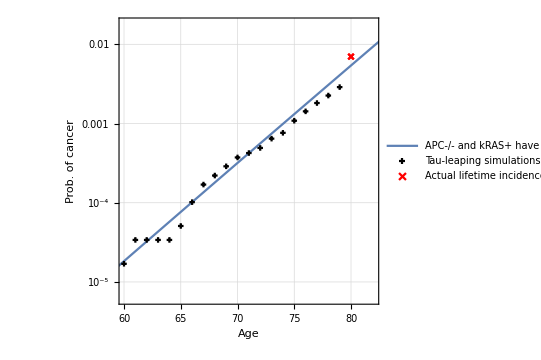

```mathematica
plot2=Show[{Curves,OldSimsPlot,Reallife},Frame-> True,Axes-> False,FrameLabel->{Style["Age",Black,14],Style["Prob. of cancer",Black,14]},PlotRange-> {{60,82},{-12,-4}},AspectRatio-> 0.9]
```

```mathematica
Export["/home/chay/Documents/Academic/Papers/Colorectal Adenocarcinoma 2019/withsims-5.pdf",plot2]
```

/home/chay/Documents/Academic/Papers/Colorectal Adenocarcinoma 2019/withsims-5.pdf